# Little Tests, One pyramidal lvl

## Start

```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{ParentDirectory[ParentDirectory[NotebookDirectory[]]],"1DPackage","*"}]
$Path=Join[$Path,FileNames[packageDirectory]];
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\1DPackage\*

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"
<<"pyramidalStereoAll`"

methods={"","OverConstrained","SemiConstrained","Constrained","ConstrainedInitialSign","ConstrainedNewMethod","ConstrainedPickierFunction"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)

baseAEREAL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Aereal",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
reduce=2;
path1=FileNameJoin[{baseAEREAL,"Aereal1.png"}];
path2=FileNameJoin[{baseAEREAL,"Aereal2.png"}];
pathResult=FileNameJoin[{baseAEREAL,"AerealResult.png"}];

rgb2d[{r_,g_,b_}]:=r*4+g/64;
clean[img_]:=Image[ImageData[img]];

reduire[img_,1]:=img;
reduire[img_,factor_]:=ImageResize[img,ImageDimensions[img]/factor];

ia=reduire[ColorConvert[clean@Import[path1],"GrayScale"],reduce];
ib=reduire[ColorConvert[clean@Import[path2],"GrayScale"],reduce];
icolor=reduire[clean@Import[pathResult],reduce];

Show[{ia,ib}]

(*{1,44},{1,102} arbitrary size to make the method faster *)
dim=ImageDimensions[ia];
nx=800/reduce;
ny=700/reduce;

{ia,ib,icolor}=ImageTake[#,{ny,ny+44},{nx,nx+102}]&/@{ia,ib,icolor}
ImageDimensions[#]&/@{ia,ib,icolor}
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-}

{{103,45},{103,45},{103,45}}

## V0

```mathematica
removeClosest[s_]:=Block[{n,c},(n=Nearest[s];
c=SortBy[Table[{i,Norm[s[[i]]-n[s[[i]],2][[2]]]},{i,1,Length[s]}],(#[[2]])&][[1,1]];
Delete[s,c])];
removeClosest[s_]:=s/;Length[s]<2;
```

```mathematica
(* Creating list of initial Values, examples *)
r=Random[];
listv0=Select[RandomReal[{-1,1},{1000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤1)&];
listv0=Nest[removeClosest,listv0,Length[listv0]-50];
ListPlot[listv0,AspectRatio->Automatic];
```

## Little functions

```mathematica
RainbowColor[z_]:=Blend[{Purple,Blue,Cyan,Green,Yellow,Orange,Red},z];
```

```mathematica
affiche[{p_,v_},y_]:={RainbowColor[Rescale[v,{-1.5,1.5},{0,1}]],Point[{p-0.5,y+0.5}]};
```

```mathematica
bigTest[steps_,e_,minmaxList_,dis_]:=Block[{ic,depth, resTable,realPVTable,pos,pv,g0},(
Table[
ic=move[ia,dis];
depth=stereoDepth[listv0,ia,ic,minmax[[2]],minmax,Range[1,103,steps],Range[1,45],e,"ConstrainedNewMethod"];

(* We only keep converged solutions *)
resTable=Table[
Select[depth[[r]],#[[2]]=="converged"&]
(*depth[[r]]*)
,{r,45}];

(* We give right coordinates to each solution *)
realPVTable=Table[
pos=resTable[[r,All,5]]-resTable[[r,All,3]];
pv=Thread[{pos,resTable[[r,All,1]]}]
,{r,45}];

(* We create g0 *)
g0=Graphics[{PointSize[0.009],Table[affiche[#,45-y]&/@realPVTable[[y]],{y,1,45}]}];
g0=Rasterize[Show[ia,g0],ImageSize->ImageDimensions[ia]*5,ImageResolution->300];

(* We only keep NON converged solutions *)
nonresTable=Table[
Select[depth[[r]],#[[2]]!="converged"&]
(*depth[[r]]*)
,{r,45}];

(* We give right coordinates to each solution *)
nonrealPVTable=Table[
pos=nonresTable[[r,All,5]]-nonresTable[[r,All,3]];
pv=Thread[{pos,nonresTable[[r,All,1]]}]
,{r,45}];

{realPVTable,g0,nonrealPVTable}

,{minmax,minmaxList}]
)]
```

## Big Tests

```mathematica
e=0.0001;
```

```mathematica
fontsize=12;
imagesize=600;
plotRange={{-0.5,1.5},{0,800}};
```

### dis=0.5

#### Full image dis=0.5

```mathematica
dis=0.5;
step=1;
```

```mathematica
(* Creating list of initial Values *)
r=Random[];
listv0=Select[RandomReal[{-step,step},{1000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤step)&];
listv0=Nest[removeClosest,listv0,Length[listv0]-50];
```

```mathematica
testList={{1,1},{1,2},{1,3},{1,4},{4,4},{3,4},{2,4},{1,4}};
Subscript[resTable^step, dis]=bigTest[1,e,testList,dis];
```

```mathematica
Dimensions[Subscript[resTable^step, dis]]
```

{8,3}

#### Density plot dis=0.5

```mathematica
dis=0.5;
step=1;
```

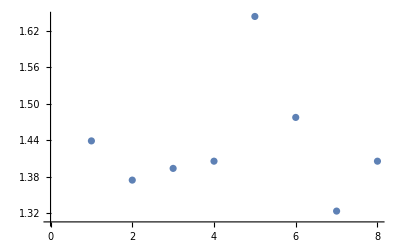

```mathematica
densityValues=Table[

p=DeleteDuplicates/@Round[res[[All,All,1]]-0.5];
pxy=Table[Thread[{r,p[[r]]}],{r,Length[p]}];
density=103.*45./Length[Flatten[pxy,1]];
rmse=Sqrt[Mean[(Flatten[res,1][[All,2]]-dis)^2]];

{density,rmse}

,{res, Subscript[resTable^step, dis][[All,1]]}];
ListPlot[Sqrt[Total/@densityValues^2]]
```

#### Display Full image dis=0.5, step=3

```mathematica
dis=0.5;
step=1;
```

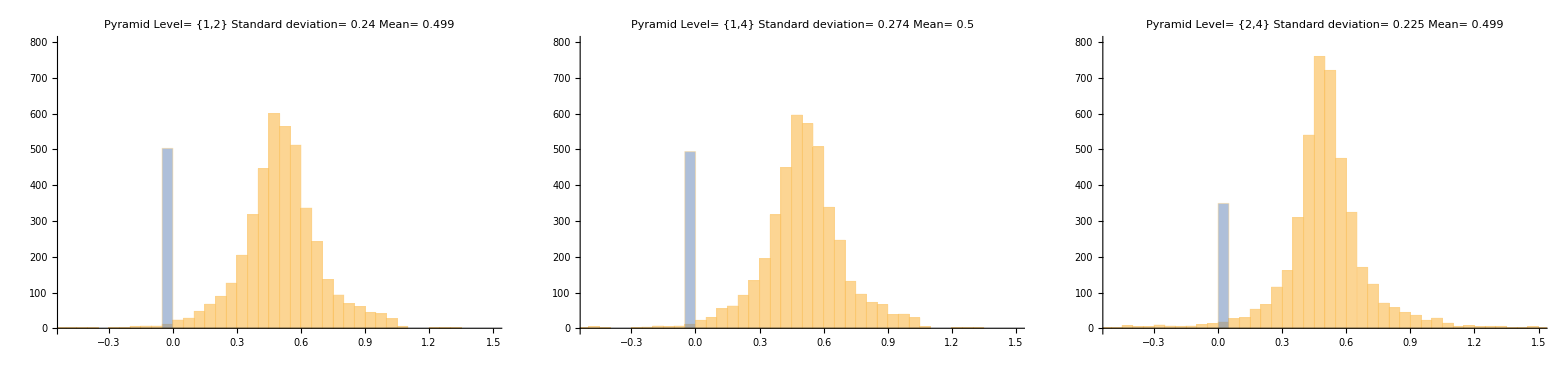

```mathematica
gFinal=
Legended[
GraphicsRow[
Table[

std=StandardDeviation[Flatten[Subscript[resTable^step, dis][[wichShow,1,All,All,2]]]];
mu=Mean[Flatten[Subscript[resTable^step, dis][[wichShow,1,All,All,2]]]];

convergedData=Flatten[Subscript[resTable^step, dis][[wichShow,1,All,All,2]]];
nonConvergedData=Flatten[Subscript[resTable^step, dis][[wichShow,3,All,All,2]]];

Subscript[h0^step, dis]=Histogram[{convergedData, nonConvergedData},
PlotLabel->Column[{
Style[Row[{"Pyramid Level= ",testList[[wichShow]]}],FontSize->fontsize,FontFamily->"Times",Italic],
Style[Row[{"Standard deviation= ",NumberForm[std,3]}],FontSize->fontsize,FontFamily->"Times",Italic],
Style[Row[{"Mean= ",NumberForm[mu,3]}],FontSize->fontsize, FontFamily->"Times",Italic]},
Spacings->0.1,Alignment->Center],
PlotRange->plotRange
]

,{wichShow,{2,4,7}}],
Spacings->0,ImageSize->1600],
Placed[SwatchLegend[{LightOrange, LightBlue},{"Converged", "Non Converged"},LegendLayout->"Row"],Below]]
```

```mathematica
figsDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"figs"}];

Export[FileNameJoin[{figsDirectory,"histogram2.pdf"}],gFinal]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\histogram2.pdf